## Profile functions in the steady flow (reconstructed)

This notebook uses different systems to repeatedly calculate results for one experimental setup. Then, the moments are used to restore the profiles of some flow quantities. The restored profiles are compared to the exact profiles at two positions on the x axis.

## Preliminaries

```mathematica
Quiet[Remove["Global`*"];
Remove/@((#<>"*")&/@Contexts[Evaluate[Context[]]]);] (* clears the scope *)
```

```mathematica
engineDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"engine"}]; (* set directory of the engine folder *)
```

```mathematica
(* load engines *)
Get[FileNameJoin[{engineDirectory,"FreeSurf.wl"}]] 
Get[FileNameJoin[{engineDirectory,"DSM0.wl"}]] 
Get[FileNameJoin[{engineDirectory,"DSM1.wl"}]] 
Get[FileNameJoin[{engineDirectory,"DSM2.wl"}]] 
Get[FileNameJoin[{engineDirectory,"DSM3.wl"}]] 
Get[FileNameJoin[{engineDirectory,"GN.wl"}]]
```

```mathematica
(* some option for nicer plots *)
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"];
```

## Set parameters

```mathematica
(* Experiment parameters *)
Fr = .6; H = .6; n = 90;η=.09; σ=.25;
(*x values for the profile plotting*)
xMin=-.2;xMax=.6;
```

## Run simulations

```mathematica
{dsm0, dsm1, dsm2, dsm3, full, gn} = (#[H, Fr,η,σ, n]) & /@ {DSM0, DSM1, DSM2, DSM3, FreeSurf, GN};
```

```mathematica
allDataLoaded[]:=AllTrue[((h[0] /.#)&/@ {dsm0,dsm1,dsm2,dsm3,full,gn}),NumericQ];
(*check if all data is there loaded*)
Clear[abort];If[!allDataLoaded[],abort=!ChoiceDialog["Some functions seem to be missing! Continue?"]];If[abort,Interrupt[],Nothing];
```

## Restore the profiles

```mathematica
(* define our first three ansatz functions *)
poly[i_,var_]:=LegendreP[i,-2var+1]
l1=poly[1,ζ];l2=poly[2,ζ];l3=poly[3,ζ];
```

```mathematica
(* restore the nonhydrostatic pressure using the moments: *)
gn=Append[gn,q->(qm[#1]+kappa1[#1] poly[1,#2]+(kappa1[#1]-qm[#1])poly[2,#2]&)];
dsm0=Append[dsm0,q->(qm[#1]&)];
dsm1=Append[dsm1,q->(qm[#1]+kappa1[#1] poly[1,#2]&)];
dsm2=Append[dsm2,q->(qm[#1]+kappa1[#1]poly[1,#2]+kappa2[#1]poly[2,#2]&)];
dsm3=Append[dsm3,q->(qm[#1]+kappa1[#1]poly[1,#2]+kappa2[#1]poly[2,#2]+kappa3[#1]poly[3,#2]&)];
```

```mathematica
(* restore the vertical velocity using the moments: *)
gn=Append[gn,w->(wm[#1]+gamma1[#1] poly[1,#2]&)];
dsm0=Append[dsm0,w->(wm[#1]&)];
dsm1=Append[dsm1,w->(wm[#1]+gamma1[#1] poly[1,#2]&)];
dsm2=Append[dsm2,w->(wm[#1]+gamma1[#1]poly[1,#2]+gamma2[#1]poly[2,#2]&)];
dsm3=Append[dsm3,w->(wm[#1]+gamma1[#1]poly[1,#2]+gamma2[#1]poly[2,#2]+gamma3[#1]poly[3,#2]&)];
```

## Plot the data

```mathematica
{wdsm0,wgn,wdsm1,wdsm2,wdsm3}={w[x,ζ],ζ} //.#&/@{dsm0,gn,dsm1,dsm2,dsm3};
```

```mathematica
{pWxMin,pWxMax}=ParametricPlot[
Evaluate[{wdsm0,wgn,wdsm1,wdsm2,wdsm3} /. x->#],{ζ,0,1},
PlotRange->{{-.2,.4},{0,1}},
AspectRatio->.5,
Axes->False,
FrameStyle->Black,
GridLines->{{-.1,{0,Directive[Black,Thick]},.1,.2,.3},Automatic},
GridLinesStyle->{Opacity[1],Black},
PlotTheme->{"Frame","BoldColor","MediumLines"},
LabelStyle->{Directive[14],Black},
ImagePadding->{{40,13},{35,10}},
PlotLegends->Placed[tag/.#&/@{dsm0,gn,dsm1,dsm2,dsm3},Right]
]& /@ {xMin,xMax};
```

```mathematica
{lpWxMin,lpWxMax}=ListPlot[Table[{w[#,ζ],ζ}/.full,{ζ,0,1,.05}],PlotMarkers->{"∘",28},PlotRange->{{-.2,.4},{0,1}},Axes->False,AspectRatio->.5,ImagePadding->{{40,13},{35,10}},PlotStyle->{Black,AbsoluteThickness[3]}]&/@{xMin,xMax};
```

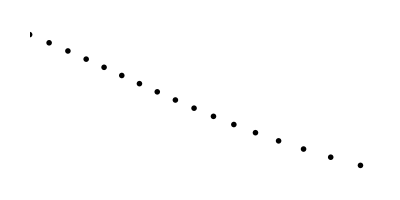
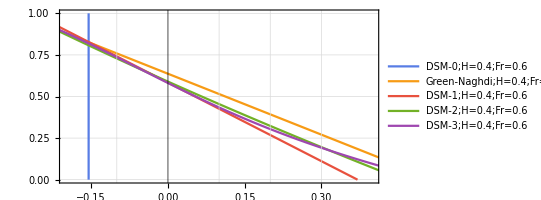

```mathematica
wxMin=Overlay[{lpWxMin,pWxMin}]
```

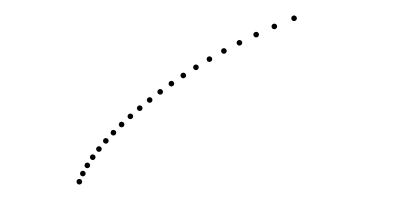
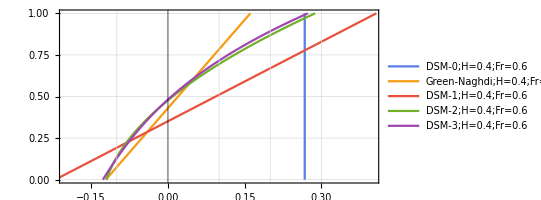

```mathematica
wxMax=Overlay[{lpWxMax,pWxMax}]
```

```mathematica
{qdsm0,qgn,qdsm1,qdsm2,qdsm3}={q[x,ζ],ζ} //.#&/@{dsm0,gn,dsm1,dsm2,dsm3};
```

```mathematica
{pQxMin,pQxMax}=ParametricPlot[
Evaluate[{qdsm0,qgn,qdsm1,qdsm2,qdsm3} /. x->#],{ζ,0,1},
PlotRange->{{-.05,0.07},{0,1}},
AspectRatio->.5,
Axes->False,
FrameStyle->Black,
GridLines->{{-.04,-.02,{0,Directive[Black,Thick]},.02,.04,.06},Automatic},
GridLinesStyle->{Opacity[1],Black},
PlotTheme->{"Frame","BoldColor","MediumLines"},
LabelStyle->{Directive[14],Black},
ImagePadding->{{40,13},{35,10}},
PlotLegends->Placed[tag/.#&/@{dsm0,gn,dsm1,dsm2,dsm3},Right]
]& /@ {xMin,xMax};
```

```mathematica
{lpQxMin,lpQxMax}=ListPlot[Table[{q[#,ζ],ζ}/.full,{ζ,0,1,.07}],PlotMarkers->{"∘",28},PlotRange->{{-.05,0.07},{0,1}},Axes->False,AspectRatio->.5,ImagePadding->{{40,13},{35,10}},PlotStyle->Black]&/@{xMin,xMax};
```

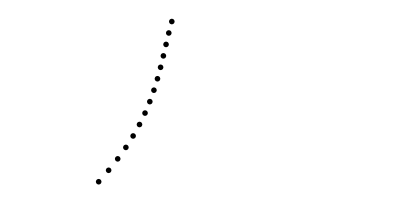
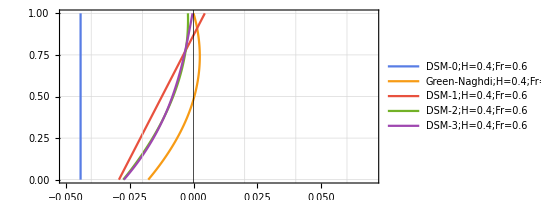

```mathematica
qxMin=Overlay[{lpQxMin,pQxMin}]
```

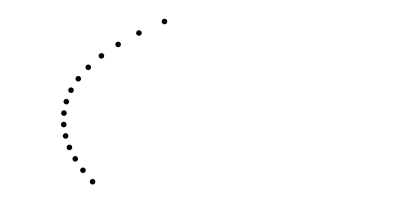
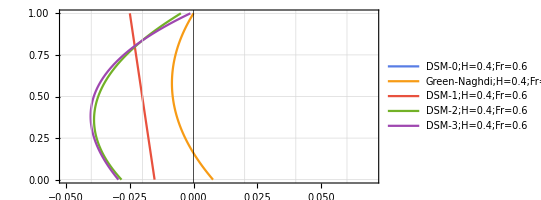

```mathematica
qxMax=Overlay[{lpQxMax,pQxMax}]
```